## extractor function

```mathematica
(*With[{dir="C:\\Users\\aliha\\Desktop\\",serial="A3",time="73",type="Nuc"},
fNames=dir<>serial<>" - "<>time<>"hrs";
ind=Flatten@StringCases[Import[fNames],x:DigitCharacter..:> FromDigits[x]];
ord=Ordering@ind;
indOrd=ind[[ord]];
(*masks=Import[dir<>serial<>" - "<>time<>"hrs\\Mask T"<>ToString[#]<>".tif"]&/@indOrd;*)
signal=Import[dir<>serial<>" - "<>time<>" hrs pp - "<>type<>".tif"][[indOrd]];
Print@Length@signal;
MapThread[
Export[dir<>"extracted images\\"<>time<>" hrs\\"<>serial<>"\\"<>type<>"\\"<>ToString[#2]<>".tif",#1]&,
{signal,indOrd}];
];*)
```

28

## preprocessing a single image

```mathematica
(* Trial on an image *)
```

```mathematica
sig=Import["C:\\Users\\aliha\\Desktop\\extracted images\\96 hrs\\A3\\Nuc\\129.tif"];
```

```mathematica
sig=ImageAdjust[sig,{0,(2^16)-1},{0,255}];
```

```mathematica
ImageType[sig]
```

Bit16

```mathematica
Image[sig,ImageSize->Medium]
```

-Graphics-

```mathematica
mask = Import["C:\\Users\\aliha\\Desktop\\extracted images\\96 hrs\\A3\\Mask\\Mask T129.tif"];
```

```mathematica
sigproc1=((ImageAdjust[TotalVariationFilter[BrightnessEqualize[#,Masking->ColorNegate@mask],0.5]]&@sig)*mask);
```

```mathematica
sigproc2=((ImageAdjust[TotalVariationFilter[BrightnessEqualize@#,0.5]]&@sig)*mask);
```

```mathematica
Image[#,ImageSize->Medium]&/@{sigproc1,sigproc2}
```

{-Graphics-,-Graphics-}

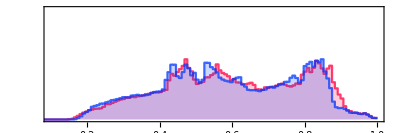

```mathematica
Show[ImageHistogram[First@#,PlotStyle->Last@#,PlotRange->{{0.1,1},Automatic}]&/@{{sigproc1,XYZColor[1,0,0,0.75]},{sigproc2,XYZColor[0,0,1,0.75]}}]
```

## preprocessing images

```mathematica
Clear@processImages;
processImages[dir_String,thresh_:0.5]:=Block[{NucsigDir,BsigDir,Nucsig,Bsig,maskDir,masks,
fileNames,order,NucsigProc,BsigProc,ind},

NucsigDir=dir<>"Nuc";maskDir=dir<>"Mask";BsigDir=dir<>"Brachyury";
ind=Flatten@StringCases[Import@maskDir,x:DigitCharacter..:> FromDigits[x]];
order=Ordering[ind];

Nucsig=Import[NucsigDir<>"\\*"];
Nucsig=ImageAdjust[#,{0,65535},{0,255}]&/@Nucsig;
Bsig=Import[BsigDir<>"\\*"];
Bsig=ImageAdjust[#,{0,65535},{0,255}]&/@Bsig;
Print[ImageType[#]&@*First/@{Bsig,Nucsig}];
masks=Import[maskDir<>"\\"<>#]&/@DeleteCases[Import[maskDir],"Thumbs.db"];

{masks,Nucsig,Bsig}={masks[[order]],Nucsig[[order]],Bsig[[order]]};

NucsigProc=MapThread[
ImageAdjust@TotalVariationFilter[BrightnessEqualize[#1,Masking->ColorNegate@#2],thresh]*#2&,{Nucsig,masks}
];
BsigProc=MapThread[
ImageAdjust@TotalVariationFilter[BrightnessEqualize[#1,Masking->ColorNegate@#2],thresh]*#2&,{Bsig,masks}
];
{Sort@ind,NucsigProc,BsigProc}
];
```

```mathematica
{ind,nucproc,brachproc}=processImages["C:\\Users\\aliha\\Desktop\\extracted images\\96 hrs\\H6\\"];
```

{Bit16,Bit16}

```mathematica
ind
```

{1,5,10,15,20,25,30,35,40,45,50,55,60,70,75}

```mathematica
(* Export image sequence *)
```

```mathematica
MapThread[
Export["C:\\Users\\aliha\\Desktop\\extracted images\\96 hrs\\H6\\Nuc-processed\\"<>ToString[#1]<>".tif",#2]&,{ind,nucproc}
];
```

```mathematica
MapThread[
Export["C:\\Users\\aliha\\Desktop\\extracted images\\96 hrs\\H6\\Brachyury-processed\\"<>ToString[#1]<>".tif",#2]&,{ind,brachproc}
];
```